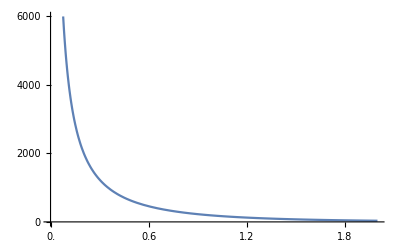

```mathematica
V[t]:=V0 Exp[-t]/t;
V0=500;
Plot[V[t],{t,0,2},PlotRange->{0,6000},Ticks->{Range[0,2,0.2],Range[0,6000,2000]}]
```

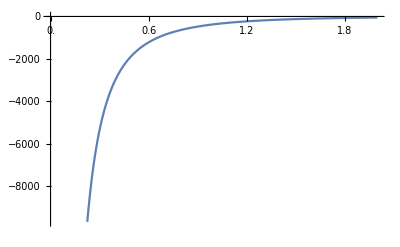

```mathematica
V[t_]:=V0 Exp[-t]/t;
V0=500;
Plot[Evaluate@D[V[t],t],{t,0,2},Ticks->{Range[0,2,0.2],Automatic}]
```